```mathematica
SetDirectory[NotebookDirectory[]];
```

## sigma phase boundary

```mathematica
fpiall=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/fpi.dat"]],{i,1,50}];
Tc=Table[Max[Table[If[1/fpiall[[j]][[i]]<1&&1/fpiall[[j]][[i+1]]>100,i,0],{i,1,Length[fpiall[[j]]]}]],{j,1,47}];
mub=Flatten[Table[i*14,{i,1,47}]];
```

```mathematica
mub2=Flatten[{mub,700.}]
```

{14,28,42,56,70,84,98,112,126,140,154,168,182,196,210,224,238,252,266,280,294,308,322,336,350,364,378,392,406,420,434,448,462,476,490,504,518,532,546,560,574,588,602,616,630,644,658,700.}

```mathematica
Tc2=Flatten[{Tc,64.8267100}];
```

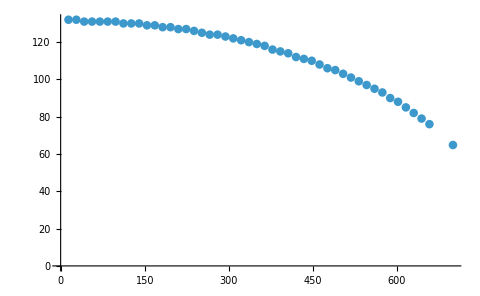

```mathematica
ListPlot[Transpose[{mub2,Tc2}],PlotRange->All]
```

```mathematica
fitpd=FindFit[Transpose[{mub2,Tc2}],a+b x^2+c x^4,{a,b,c},x]
```

{a→131.411,b→-0.0000900599,c→-8.7851×10^-11}

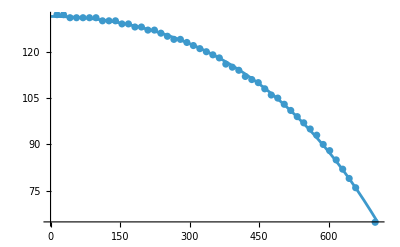

```mathematica
Show[Plot[a+b x^2+c x^4/.fitpd,{x,0,705}],ListPlot[Transpose[{mub2,Tc2}]]]
```

```mathematica
phaseboundary=Table[{x,a+b x^2+c x^4/.fitpd},{x,0,700,10}];
```

```mathematica
Export["pb.dat",phaseboundary]
```

pb.dat